### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->2,U1->5,U2->6, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

(Maybe the) system is not feasible!

            	Check the paper: The current method for stationary mean-field games on networks

{1.32698,Null}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->6, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.068575 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.095537,Null}

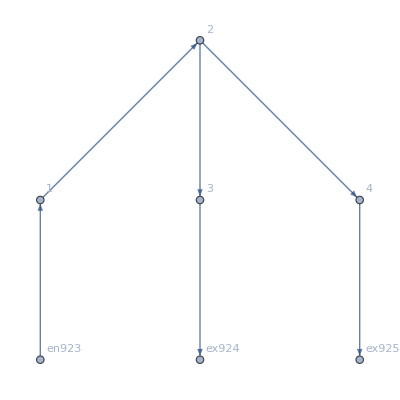

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→10.,u951→6.,u952→7.,u953→5.,u954→6.,u955→10.,u956→8.,u957→5.,u958→6.,u959→5.,u960→6.,u961→10.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→8.75229,u951→5.70576,u952→6.70576,u953→5.,u954→6.,u955→8.75229,u956→7.70576,u957→5.,u958→6.,u959→5.,u960→6.,u961→8.75229|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→8.82592,u951→5.72685,u952→6.72685,u953→5.,u954→6.,u955→8.82592,u956→7.72685,u957→5.,u958→6.,u959→5.,u960→6.,u961→8.82592|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.66105×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.66105×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→8.99482,u951→5.77321,u952→6.77321,u953→5.,u954→6.,u955→8.99482,u956→7.77321,u957→5.,u958→6.,u959→5.,u960→6.,u961→8.99482|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.08768×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.97873×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→9.79269,u951→5.9592,u952→6.9592,u953→5.,u954→6.,u955→9.79269,u956→7.9592,u957→5.,u958→6.,u959→5.,u960→6.,u961→9.79269|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.71948×10^-15,ComplexInfinity]

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→10.,u951→6.,u952→7.,u953→5.,u954→6.,u955→10.,u956→8.,u957→5.,u958→6.,u959→5.,u960→6.,u961→10.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.08779×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.30815×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→10.5367,u951→6.0941,u952→7.0941,u953→5.,u954→6.,u955→10.5367,u956→8.0941,u957→5.,u958→6.,u959→5.,u960→6.,u961→10.5367|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94291×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94291×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→11.9217,u951→6.27899,u952→7.27899,u953→5.,u954→6.,u955→11.9217,u956→8.27899,u957→5.,u958→6.,u959→5.,u960→6.,u961→11.9217|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.7184×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.23458×10^-15

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→12.7031,u951→6.35738,u952→7.35738,u953→5.,u954→6.,u955→12.7031,u956→8.35738,u957→5.,u958→6.,u959→5.,u960→6.,u961→12.7031|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.91346×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.53085×10^-15

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→15.5434,u951→6.55247,u952→7.55247,u953→5.,u954→6.,u955→15.5434,u956→8.55247,u957→5.,u958→6.,u959→5.,u960→6.,u961→15.5434|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.14948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.11279×10^-15

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→18.5708,u951→6.6767,u952→7.6767,u953→5.,u954→6.,u955→18.5708,u956→8.6767,u957→5.,u958→6.,u959→5.,u960→6.,u961→18.5708|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.32456×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.30965×10^-16

<|j926→2.,j927→1.,j928→1.,j929→1.,j930→1.,j931→2.,j932→0.,j933→0.,j934→0.,j935→0.,j936→0.,j937→0.,jt938→0.,jt939→2.,jt940→1.,jt941→1.,jt942→0.,jt943→0.,jt944→0.,jt945→0.,jt946→1.,jt947→0.,jt948→1.,jt949→0.,u950→25.1999,u951→6.82668,u952→7.82668,u953→5.,u954→6.,u955→25.1999,u956→8.82668,u957→5.,u958→6.,u959→5.,u960→6.,u961→25.1999|>